```mathematica
v0 = 0.2 ; 
Tmax :=  40 ;
exp = 2.002;
```

```mathematica
orbit = NDSolve[
{x''[t] + x[t]/(x[t]^2 + y[t]^2)^(exp - 0.5) == 0, y''[t] + y[t]/(x[t]^2 + y[t]^2)^(exp - 0.5) == 0,
 x[0] == 1, 
y[0] == 0, 
x'[0] == 0, 
y'[0] == v0}, 
{x, y}, 
{t, 0, Tmax}
 ]
```

{{x→InterpolatingFunction[{{0.,40.}},<>],y→InterpolatingFunction[{{0.,40.}},<>]}}

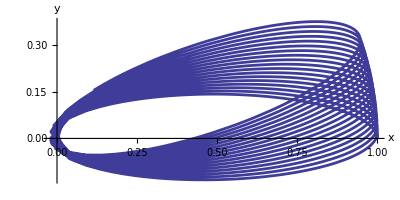

```mathematica
ParametricPlot[
Evaluate[{x[t],y[t]}/.orbit],
{t,0,Tmax},
AspectRatio->Automatic,
AxesLabel->{"x","y"},
PlotStyle->{AbsoluteThickness[2]}]
```